```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"]];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
Print["Runs in the list: runNum = ",runNum={12695}]
Print["#Runs in the list: runn = ",runn=Dimensions[runNum][[1]]];
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;ChNum=4;binw=10;
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Runs in the list: runNum = {12695}

#Runs in the list: runn = 1

```mathematica
nlmud["MeanPredictionBands",ConfidenceLevel->.90][[1]]
nlmud["MeanPredictionBands",ConfidenceLevel->.90][[2]]
```

24.0063+23.456 ⅇ^(-0.00875828 xx)-1.65291 √(ⅇ^(-0.0262748 xx) (0.452 ⅇ^(0.0262748 xx)+ⅇ^(0.0175166 xx) (14.9831-0.0949125 xx)+ⅇ^(0.00875828 xx) (142.465-1.71421 xx+0.00526273 xx^2)))

24.0063+23.456 ⅇ^(-0.00875828 xx)+1.65291 √(ⅇ^(-0.0262748 xx) (0.452 ⅇ^(0.0262748 xx)+ⅇ^(0.0175166 xx) (14.9831-0.0949125 xx)+ⅇ^(0.00875828 xx) (142.465-1.71421 xx+0.00526273 xx^2)))

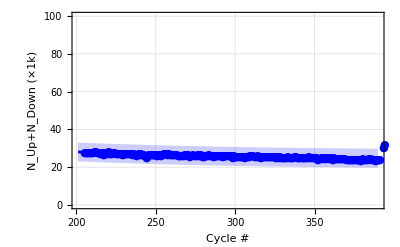
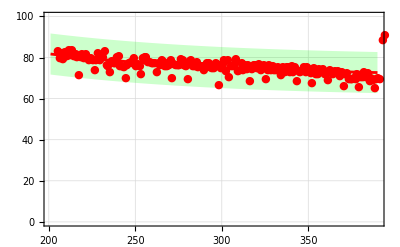

```mathematica
runi=1;
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta5.edm"],metaStructure2];
begCy=201;
maxCy=390;
ptud=Table[{data[[k]][[2]],{data[[k]][[27]]+data[[k]][[28]],Sqrt[data[[k]][[27]]+data[[k]][[28]]]}/1000},{k,begCy,maxCy}];
ptmon=Table[{data[[k]][[2]],{data[[k]][[30]],Sqrt[data[[k]][[30]]]}/10000},{k,begCy,maxCy}];
ptudmon=Table[{data[[k]][[2]],{(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]],((Sqrt[data[[k]][[27]]+data[[k]][[28]]])/data[[k]][[30]]+(Sqrt[data[[k]][[30]]]*(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]^2))}},{k,begCy,maxCy}];
ftud=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/1000},{k,begCy,maxCy}];
ftmon=Table[{data[[k]][[2]],(data[[k]][[30]])/10000},{k,begCy,maxCy}];
ftudmon=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]},{k,begCy,maxCy}];
nlmud=NonlinearModelFit[ftud,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
nlmmon=NonlinearModelFit[ftmon,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
nlmudmon=NonlinearModelFit[ftudmon,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
pt1=Show[{Plot[{nlmud[xx],nlmud[xx]+5,nlmud[xx]-5},{xx,begCy,maxCy},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{{Blue,Thickness[.005]},None,None},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},
{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptud,PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{Blue},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt2=Show[{
Plot[{nlmmon[xx],nlmmon[xx]+10,nlmmon[xx]-10},{xx,begCy,maxCy},Filling->{2->{3}},FillingStyle->{Opacity[.5],Green},PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{{Red,Thickness[.005]},None,None},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptmon,PlotRange->{{begCy,maxCy},{0,100}},PlotStyle->{Red},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt3=Overlay[{pt1,pt2},ImageSize->1200]
```

```mathematica
nlmmon["ParameterTable"]
nlmmon["ANOVATable"]
nlmmon["BestFitParameters"]
nlmmon["ParameterErrors"]
nlmud["ParameterTable"]
nlmud["ANOVATable"][[1]]
nlmud["ANOVATable"][[1]][[1]][[3]][[4]]
```

| Estimate | Standard Error | t-Statistic | P-Value
aa | 70.8942 | 2.20155 | 32.2019 | 3.24965×10^-78
bb | 73.2139 | 56.0809 | 1.30551 | 0.193324
cc | 0.00950918 | 0.00440497 | 2.15874 | 0.0321447

| DF | SS | MS
Model | 3 | 1.09106×10^6 | 363686.
Error | 187 | 2173.2 | 11.6214
Uncorrected Total | 190 | 1.09323×10^6 | 
Corrected Total | 189 | 3325.29 |

{aa→70.8942,bb→73.2139,cc→0.00950918}

{2.20155,56.0809,0.00440497}

| Estimate | Standard Error | t-Statistic | P-Value
aa | 24.0531 | 0.663378 | 36.2585 | 1.58967×10^-86
bb | 24.7109 | 13.728 | 1.80003 | 0.0734671
cc | 0.00903473 | 0.00327856 | 2.7557 | 0.00643622

| DF | SS | MS
Model | 3 | 127748. | 42582.6
Error | 187 | 163.417 | 0.87389
Uncorrected Total | 190 | 127911. | 
Corrected Total | 189 | 317.663 |

0.87389

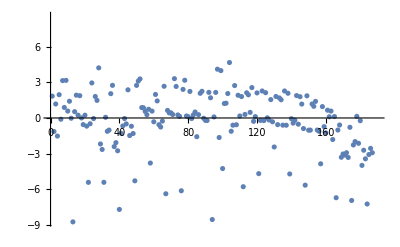

```mathematica
ListPlot[nlmmon["FitResiduals"]]
```

-4.86161×10^-16

0.929862

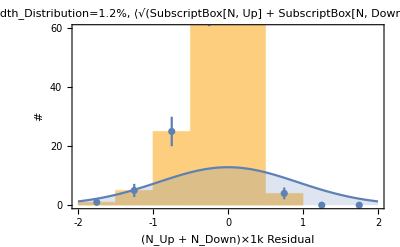

```mathematica
rmsptdatratio=Mean[nlmud["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmud["FitResiduals"]]
errptsptres=nlmud["FitResiduals"];
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Up + N_Down)×1k Residual","#"},Axes->False,PlotRange->{{-2,2},{0,60}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{32,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmud["FitResiduals"]]],2]],"%, ⟨√(SubscriptBox[N, Up]  +  SubscriptBox[N, Down])⟩^-1=",ToString[SetPrecision[100*Mean[ptud[[;;,2]][[;;,2]]/ptud[[;;,2]][[;;,1]]],2]],"%"]],
Plot[30PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,-2,2},Axes->False,PlotRange->{{-2,2},{0,60}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Up + N_Down)×1k Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-2,2},{0,60}}, Frame->True,FrameLabel->{"(N_Up + N_Down)×1k Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

```mathematica
sdptdatratio
Mean[ptud[[;;,2]][[;;,2]]]
```

0.929862

0.16093

-4.56243×10^-15

3.39093

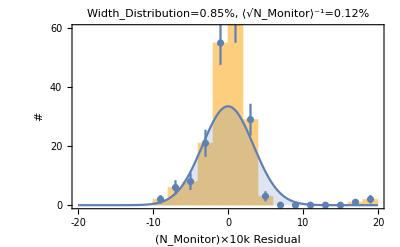

```mathematica
rmsptdatratio=Mean[nlmmon["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmmon["FitResiduals"]]
errptsptres=nlmmon["FitResiduals"];
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Monitor)×10k Residual","#"},Axes->False,PlotRange->{{-20,20},{0,60}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{32,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmmon["FitResiduals"]]],2]],"%, ⟨√N_Monitor⟩^-1=",ToString[SetPrecision[100*Mean[ptmon[[;;,2]][[;;,2]]/ptmon[[;;,2]][[;;,1]]],2]],"%"]],
Plot[285PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,-20,20},Axes->False,PlotRange->{{-20,20},{0,60}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Monitor)×10k Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-2,2},{0,60}}, Frame->True,FrameLabel->{"(N_Monitor)×10k Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

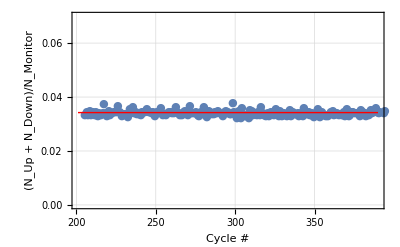

```mathematica
pt4=Show[{
EDAListPlot[ptudmon,PlotRange->{{begCy,maxCy},{0,0.07}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[nlmudmon[x],{x,begCy,maxCy},PlotRange->{{begCy,maxCy},{0,0.07}},PlotStyle->{Red,Thick},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"x","y"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}]
},ImagePadding->125]
```

-2.25331×10^-17

0.000922521

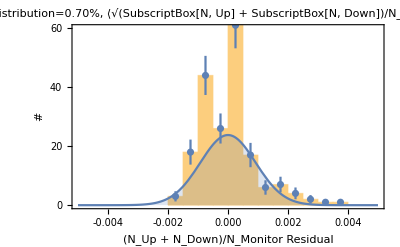

```mathematica
rmsptdatratio=Mean[nlmudmon["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmudmon["FitResiduals"]]
errptsptres=nlmudmon["FitResiduals"];
inset=Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},Axes->False,PlotRange->{{-.005,.005},{0,60}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{31,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmudmon["FitResiduals"]]],2]],"%, ⟨√(SubscriptBox[N, Up]  +  SubscriptBox[N, Down])/N_Monitor⟩^-1=",ToString[SetPrecision[100*Mean[ptudmon[[;;,2]][[;;,2]]/ptudmon[[;;,2]][[;;,1]]],2]],"%"]],
Plot[0.055PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,-.005,.005},Axes->False,PlotRange->{{-.005,.005},{0,60}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-.005,.005},{0,60}}, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

```mathematica
Mean[ptud[[;;,2]][[;;,2]]/(1*ptmon[[;;,2]][[;;,1]])]
Mean[ptudmon[[;;,2]][[;;,2]]]
```

0.00212747

0.000252122

7.24809×10^-17

0.000857687

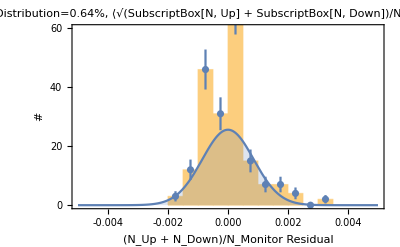

```mathematica
ptudmon2=Table[{data[[k]][[2]],{(data[[k]][[27]]+data[[k]][[28]])/(data[[k]][[27]]+data[[k]][[28]]+data[[k]][[30]]),((Sqrt[data[[k]][[27]]+data[[k]][[28]]])/data[[k]][[30]]+(Sqrt[data[[k]][[30]]]*(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]^2))}},{k,begCy,maxCy}];
ftudmon2=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/(data[[k]][[27]]+data[[k]][[28]]+data[[k]][[30]])},{k,begCy,maxCy}];
nlmudmon2=NonlinearModelFit[ftudmon2,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
rmsptdatratio=Mean[nlmudmon2["FitResiduals"]]
sdptdatratio=StandardDeviation[nlmudmon2["FitResiduals"]]
errptsptres=nlmudmon2["FitResiduals"];
Show[{
Histogram[errptsptres, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},Axes->False,PlotRange->{{-.005,.005},{0,60}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{31,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},PlotLabel->StringJoin["Width_Distribution=",ToString[SetPrecision[100*sdptdatratio/Total[Abs[nlmudmon["FitResiduals"]]],2]],"%, ⟨√(SubscriptBox[N, Up]  +  SubscriptBox[N, Down])/N_Monitor⟩=",ToString[SetPrecision[100*Mean[ptudmon[[;;,2]][[;;,2]]/ptudmon[[;;,2]][[;;,1]]],2]],"%"]],
Plot[0.055PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,-.005,.005},Axes->False,PlotRange->{{-.005,.005},{0,60}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[Table[{HistogramList[errptsptres][[1]][[k]]-(HistogramList[errptsptres][[1]][[1]]-HistogramList[errptsptres][[1]][[2]])/2,{HistogramList[errptsptres][[2]][[k]],Sqrt[HistogramList[errptsptres][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres][[2]]][[1]]}],PlotRange->{{-.005,.005},{0,60}}, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

## Extras: Appendix

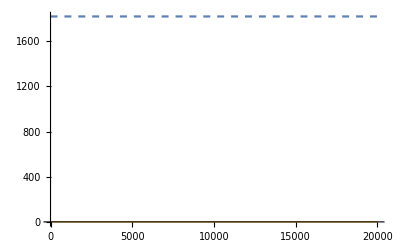

```mathematica
n1=10000;
n2=20000;
tau1=12;
tau2=880;
nud[ts_,nn_]:=nn NIntegrate[Exp[-t/tau1],{t,0,ts}]NIntegrate[Exp[-t/tau2],{t,0,180}];
nmon[ts_,nn_]:=nn NIntegrate[Exp[-t/tau1],{t,ts,ts+180}];
Plot[{nud[30,nn]/nmon[30,nn],nud[30,nn]/(nud[30,nn]+nmon[30,nn])},{nn,1,n2},PlotStyle->{Dashed,Thick}]
```